```mathematica
v1[x_,t_, C_] = (-1/2-C/2/Sqrt[C^2+4])*Exp[(x-C*t)/2*(-C+Sqrt[C^2+4])]+1;
v2[x_,t_,C_] = (1/2-C/2/Sqrt[C^2+4])*Exp[-(x-C*t)/2*(C+Sqrt[C^2+4])];
gif = Table[Plot[Piecewise[{{v1[x,t,1],x<t},{v2[x,t,1],x>=t}}],{x,0,100}, PlotRange->All, AxesLabel->{"x, length", "v, voltage"}, PlotLabel->"Bistable Membrane with Ion Channels, c=1", ImageSize->Large],{t,0,100,1}];

Export["TravelingWaveSol.gif",gif]
```

TravelingWaveSol.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["TravelingWaveSol.gif"]]]
```

```mathematica
G[x_,t_] = (4*Pi*t)^(-1/2)*Exp[-t-x^2/4/t]*HeavisideTheta[t];
gif2 = Table[Plot[G[x,t],{x,0,100}, PlotRange->{0,1}, AxesLabel->{"x, length", "v, voltage"}, PlotLabel->"Passive Membrane", ImageSize->Large],{t,0.001,5,.1}];

Export["PassiveMembrane.gif",gif2]
```

PassiveMembrane.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["TravelingWaveSol2.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["TravelingWaveSol2.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["TravelingWaveSol2.gif"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["TravelingWaveSol2.gif"]]]
```

-Graphics3D-

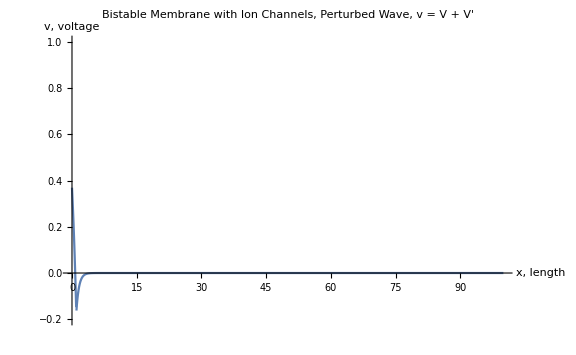
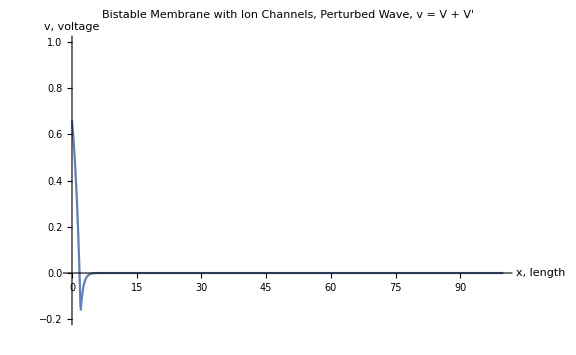
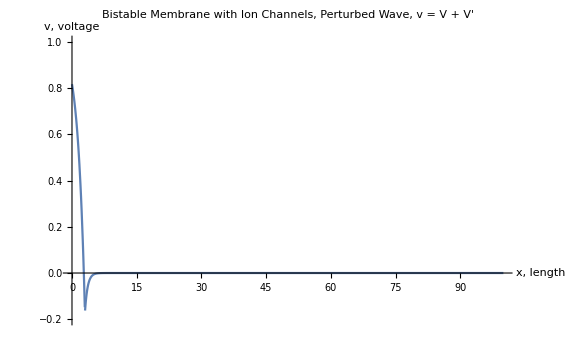
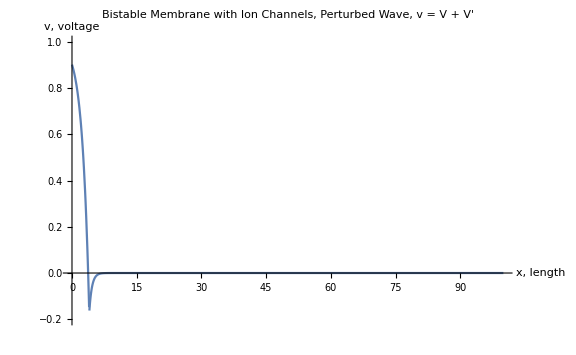
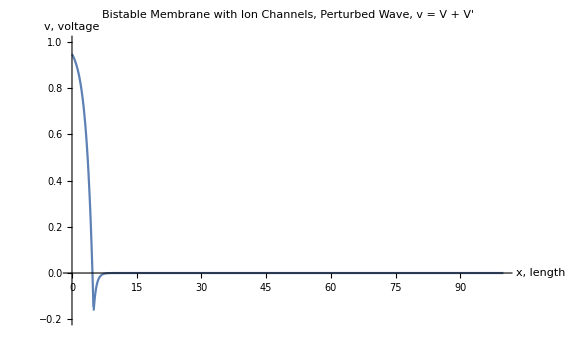
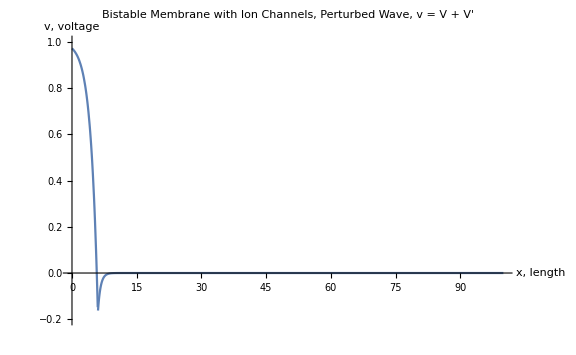
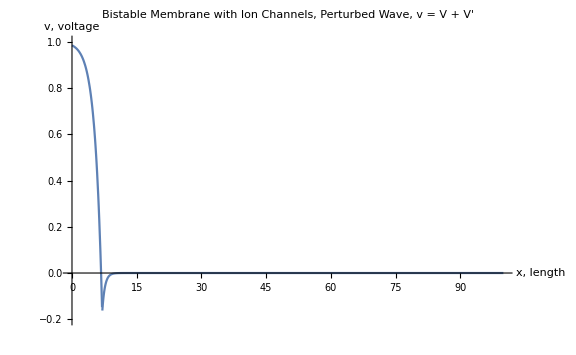
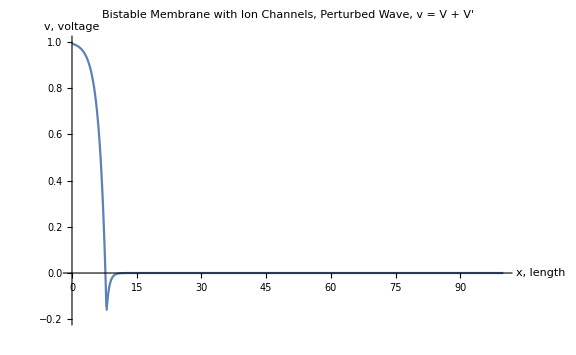

Perturbation.gif

```mathematica
dv1[x_, t_, C_] = D[v1[x,t,C],x];
dv2[x_, t_,C_] = D[v2[x,t,C],x];

Plot3D[Piecewise[{{dv1[x,t,1],x<t},{dv2[x,t,1],x>=t}}],{x,-10,10},{t,0,10}, ColorFunction->"AlpineColors", AxesLabel->Automatic]

gif3 = Table[Plot[Piecewise[{{v1[x,t,1]+dv1[x,t,1],x<t},{v2[x,t,1]+dv2[x,t,1],x>=t}}],{x,0,100}, PlotRange->{-0.2,1}, AxesLabel->{"x, length", "v, voltage"}, PlotLabel->"Bistable Membrane with Ion Channels, Perturbed Wave, v = V + V'", ImageSize->Large],{t,1,100,1}]

Export["Perturbation.gif",gif3]
```